```mathematica
ParametricPlot3D[{Exp[-1 t], Exp[-2 t], Exp[-3t]}, {t, 0, 2}]
```

-Graphics3D-

```mathematica
func[x_]:=x
Clear[a]
cE[a_, s_]:= Expectation[func[x]*(x - a), Distributed[x, NormalDistribution[a, s]]]
cV[a_, s_] := Expectation[(func[x] * (x - a) - cE[a, s])^2, Distributed[x, NormalDistribution[a, s]]]
cV[a, s]/s^4
```

(a^2 s^2+2 s^4)/s^4

```mathematica
gradientEstimatePoint[x_] := func[x]*(x - mu)
estimator[X_] := Map[func, X].(X - Table[mu, Length[X]])/(s^2*Length[X])
estimatorCV[X_] := Map[func, X].(X - Table[Mean[X], Length[X]])/(s^2*Length[X]);
numSamples= 50;
cov := s^2*IdentityMatrix[numSamples];
Expectation[estimator[Array[x, numSamples]],Distributed[Array[x,numSamples], MultinormalDistribution[Table[mu, numSamples], cov]]]
Expectation[(estimator[Array[x, numSamples]] - 1)^2,Distributed[Array[x,numSamples], MultinormalDistribution[Table[mu, numSamples], cov]]]
Expectation[estimatorCV[Array[x, numSamples]],Distributed[Array[x,numSamples], MultinormalDistribution[Table[mu, numSamples], cov]]]
Expectation[(estimatorCV[Array[x, numSamples]] - 9/10)^2,Distributed[Array[x,numSamples], MultinormalDistribution[Table[mu, numSamples], cov]]]
Simplify[estimatorCV[Array[x, 5]]]
```

1

(mu^2+2 s^2)/(50 s^2)

49/50

57/1250

1/(25 s^2)(4 x[1]^2+4 x[2]^2+4 x[3]^2-2 x[3] x[4]+4 x[4]^2-2 x[3] x[5]-2 x[4] x[5]+4 x[5]^2-2 x[2] (x[3]+x[4]+x[5])-2 x[1] (x[2]+x[3]+x[4]+x[5]))

```mathematica
meanFun[{1,2,3}]
a = {1,2 , 3};
Total[a] / Length[a]
```

meanFun[{1,2,3}]

2

```mathematica
BetaDistribution
```

```mathematica
{-1,-1}
```

```mathematica
Expectation[x[1]^2 * x[2]^2,
```

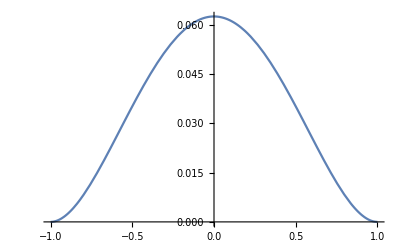

```mathematica
Plot[(x / 2 + 1/2)^2 (1/2 - x/2)^2, {x, -1, 1}]
```

```mathematica
e4 = Simplify[Expectation[(2R(u - 1/2))^4, Distributed[u, BetaDistribution[a, a]]]]
e2=Simplify[Expectation[(2R(u - 1/2))^2, Distributed[u, BetaDistribution[a, a]]]]
```

(3 R^4)/(3+8 a+4 a^2)

R^2/(1+2 a)

```mathematica
v1 = Simplify[2(t - e2)/(e4)]
```

(2 (-1+2 a) (-R^2+(-3+2 a) t))/(3 R^4)

```mathematica
gg = (a - 1)/(2 R^2) (4 (2a - 1)(2a - 3))/((a - 2)(a-1))(t/(2R^2) (a  - 3/2)- 1/4)
v2 = Simplify[gg]
```

(2 (-3+2 a) (-1+2 a) (-1/4+((-3/2+a) t)/(2 R^2)))/((-2+a) R^2)

((-3+2 a) (-1+2 a) (-R^2+(-3+2 a) t))/(2 (-2+a) R^4)

```mathematica
v1 - v2
```

((-1+2 a) (-R^2+(-3+2 a) t))/(6 R^4)-((-1+a) (-1+2 a) (-R^2+(-3+2 a) t))/(a R^4)

```mathematica
Simplify[u^2/(2R^2) (a - 3/2) - 1/4]
```

1/4 (-1+((-3+2 a) u^2)/R^2)

```mathematica
Simplify[(a - 2)/(2R^2) u^2 - (1/4 - u^2/(4R^2))]
```

1/4 (-1+((-3+2 a) u^2)/R^2)

```mathematica
f[x_, x0_, R_, a_] := 1/Beta[a, a] * (1/2 + (x - x0)/(2R))^(a - 1)(1/2 - (x - x0)/(2R))^(a - 1);
Simplify[D[f[x, x0, R, a], {x0}]]
Simplify[D[f[x, x0, R, a], {x0, 2}]]
```

(2^(3-2 a) (-1+a) R^2 (x-x0) (((R+x-x0) (R-x+x0))/R^2)^a)/((R+x-x0)^2 (R-x+x0)^2 Beta[a,a])

(2^(3-2 a) (-1+a) R^2 (-R^2+(-3+2 a) (x-x0)^2) (((R+x-x0) (R-x+x0))/R^2)^a)/((R+x-x0)^3 (R-x+x0)^3 Beta[a,a])

```mathematica
(2^(3-2 a) (-1+a) R^2 (-R^2+(-3+2 a) (x-x0)^2) (((R+x-x0) (R-x+x0))/R^2)^a)/((R+x-x0)^3 (R-x+x0)^3 Beta[a,a])
```

```mathematica
(2^-3 (-1+a) (-R^2+(-3+2 a) (x-x0)^2) (((R+x-x0) (R-x+x0))/(4 R^2))^(a-3))/(R^4 Beta[a,a])
```

```mathematica
(2^-3 (-1+a) (-R^2+(-3+2 a) (x-x0)^2))/(R^4 Beta[a,a])
```

```mathematica
haha = (2^-3 (-1+a) (-R^2+(-3+2 a) (x-x0)^2))/R^4/( (a - 1)(a - 2))^2*((2a - 1)(2a - 2)(2a - 3)(2a - 4))
Simplify[haha]
```

((-4+2 a) (-3+2 a) (-2+2 a) (-1+2 a) (-R^2+(-3+2 a) (x-x0)^2))/(8 (-2+a)^2 (-1+a) R^4)

((-3+2 a) (-1+2 a) (-R^2+(-3+2 a) (x-x0)^2))/(2 (-2+a) R^4)

```mathematica
(32 (-3+2 a) (-1+2 a) (-R^2+(-3+2 a) (x-x0)^2))/((-2+a) R^4)
```

(32 (-3+2 a) (-1+2 a) (-R^2+(-3+2 a) (x-x0)^2))/((-2+a) R^4)

```mathematica
((-3+2 a) (-1+2 a) (-R^2+(-3+2 a) t))/(2 (-2+a) R^4)
```

((-3+2 a) (-1+2 a) (-R^2+(-3+2 a) t))/(2 (-2+a) R^4)

```mathematica
Beta[2, 2]
```

1/6